### Figure 2a: Tumor trajectories

```mathematica
dir=NotebookDirectory[]<>"trajectoryData/";
tumorTrajectory[filename_,xRangeMax_,style_,o_]:=Module[
{data,lengthData,stratifiedData,xTix},
data=Flatten[Import[dir<>filename,"Data"],1];
lengthData =Length[data]/4;
stratifiedData={data[[4(#-1)+1]],data[[4(#-1)+2]],data[[4(#-1)+3]],data[[4(#-1)+4]]}&/@Range[1,lengthData];
xTix={{0,"0"},{30,"30"},{60,"60"},{90,"90"},{120,"120"},{150,"150"},{180,"180"}};
ListLogPlot[
{stratifiedData[[#,1]],stratifiedData[[#,-1]]}&/@Range[1,lengthData],
PlotStyle->style,
Joined->True,
(*Filling->Bottom,*)
PlotRange->{{-2.5,xRangeMax-5}1.05,{0.25,0.3*10^13}},
GridLines->{{},{100}},
GridLinesStyle->Directive[Dashed, Black,Thickness[0.002]],
FrameLabel->{"Days post CAR infusion","CD19^+ tumor cells"},
FrameStyle->Directive[Thickness[0.0025],Black],
Frame->{{True,False},{True,False}},
AspectRatio->0.45,
ImageSize->500,
FrameTicks->{{{{10^12,"10^12"},{10^10,"10^10"},{10^8,"10^8"},{10^6,"10^6"},{10^4,"10^4"},{10^2,"10^2"},{10^0,"1"}},None},{xTix,None}},
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
PlotLegends->Placed[{""},o]
]
]
```

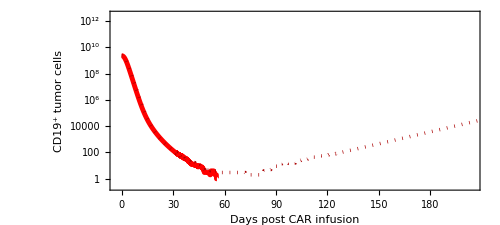

```mathematica
plotTrajectory=Show[
tumorTrajectory["trajectory_6_2020-09-14.dat",200,{Thickness[0.007],Red},{0.65,0.9}],
tumorTrajectory["trajectory_8_2020-09-14.dat",200,{Thickness[0.005],Darker[Red],Dotted},{0.65,0.75}]
]
```

```mathematica
Export[NotebookDirectory[]<>"Tumor01.pdf",plotTrajectory,"PDF"]
```

/Users/gregorykimmel/Dropbox/_Projects/01_CART/_Kimmel et al/_gitRepo/hybridModelRuns/Tumor01.pdf

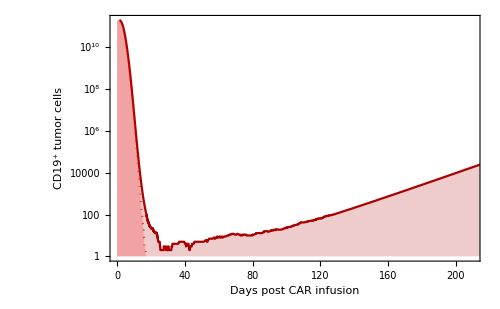

```mathematica
(* 
"trajectory_41_2019-06-25.dat" has stochastic region to eventual relapse and growth
"trajectory_21_2019-06-25.dat" has stochastic region to eventual cure.
You can check from 1 to 100 to see if you find one you like better
 *)
```

```mathematica
Export[NotebookDirectory[]<>"tumorTrajectories.pdf",plotTrajectory,"PDF"]
```

/Users/gregorykimmel/Dropbox/_Projects/01_CART/code/hybridModelRuns/tumorTrajectories.pdf

```mathematica
(* 4, 10,16,18 *)
```

```mathematica
Figure 2b: Durable response 800 days from infusion as a function of CAR memory frequency
```

```mathematica
(* This module creates a K-M curve using the given filename *)
dir=NotebookDirectory[]<>"runData/";
makeSurvivalCurve[filename_]:=Module[
{data,patients,time,ci,S},
data=Import[dir<>filename,"Data"];
patients = data[[4;;]]; (* The first 3 lines contain parameter info *)
time={};
(* We now loop over all patients and look to see when progression occurs (we add large number to cure so it will never show progression in the K-M curve). *)
For[n=1,n≤ Length[patients],n++,
If[patients[[n,2]]=="cure",AppendTo[time,patients[[n,1]]+10000],AppendTo[time,patients[[n,1]]]]];
ci=0&/@Range[Length[time]];
S=SurvivalModelFit[EventData[time,ci]];
{time,ci,patients,S}
]
nStart=21;
nEnd=31;
nFiles = nEnd-nStart+1;
date="2019-11-20";
(*Do[If[FileExistsQ[dir<>"outputData_"<>ToString[n]<>"_"<>date<>".txt"],nFiles=n-nStart+1,Break[]],{n,nStart,100}]*)
memFracSurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nStart,nEnd];
memFracPFSrB065={(#-1) 0.1,(memFracSurvivalCurves[[#]][800])}&/@Range[1,nFiles];
nStart=12;
nEnd=22;
nFiles = nEnd-nStart+1;
date="2019-11-21";
(*Do[If[FileExistsQ[dir<>"outputData_"<>ToString[n]<>"_"<>date<>".txt"],nFiles=n-nStart+1,Break[]],{n,nStart,100}]*)
memFracSurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nStart,nEnd];

memFracPFSrB165={(#-1) 0.1,(memFracSurvivalCurves[[#]][800])}&/@Range[1,nFiles];

rBlegend=("r_B = "<>ToString[#]<>"/day")&/@{0.065,0.165}

(* This function makes a survival curve as a function of the memory fraction *)
L1[SurvivalCurve_,c_,i_]:=ListPlot[SurvivalCurve,
PlotRange->{{-0.035,1.035},{-0.075,1.075}},
(*GridLines->{{},{1.0}},*)
PlotStyle->Directive[c,PointSize->0.025],
PlotLegends->Placed[SwatchLegend[{rBlegend[[i]]},LegendMarkerSize->10,LegendMarkers->"Bubble"],{0.2,0.75}],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"}
,Frame->{{True,False},{True,False}}
,AspectRatio->0.325
,ImageSize->500
,FrameStyle->Directive[Thickness[0.0035],Black]
,LabelStyle->{FontSize->18,Black,FontFamily->"Arial"}
, FrameLabel->{"Fraction of CAR memory cells at infusion","Probability of CR"},
FrameTicks->{{0,0.2,0.4,0.6,0.8,1.0},{0,0.5,1.0,{0.25,""},{0.75,""}}}
];
```

{r_B = 0.065/day,r_B = 0.165/day}

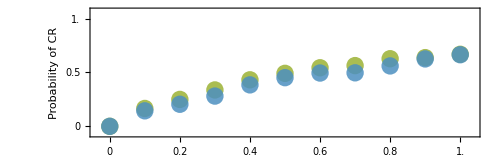

/Users/altrock/Dropbox/Projects_Dropbox/CART/code/hybridModelRuns/CARmem_Prob01.pdf

```mathematica
CARMemPFS={L1[memFracPFSrB065,ColorData["Rainbow"][0.6],1],L1[memFracPFSrB165,Opacity[0.85,ColorData["Rainbow"][0.3]],2]};
fig2mem=Show[CARMemPFS]
Export[NotebookDirectory[]<>"CARmem_Prob01.pdf",fig2mem,"PDF"]
```

```mathematica
Figure 2c: Durable response 800 days from infusion as a function of wildtype
```

```mathematica
(* This module creates a K-M curve using the given filename *)
dir=NotebookDirectory[]<>"runData/";
makeSurvivalCurve[filename_]:=Module[
{data,patients,time,ci,S},
data=Import[dir<>filename,"Data"];
patients = data[[4;;]]; (* The first 3 lines contain parameter info *)
time={};
(* We now loop over all patients and look to see when progression occurs (we add large number to cure so it will never show progression in the K-M curve). *)
For[n=1,n≤ Length[patients],n++,
If[patients[[n,2]]=="cure",AppendTo[time,patients[[n,1]]+10000],AppendTo[time,patients[[n,1]]]]];
ci=0&/@Range[Length[time]];
S=SurvivalModelFit[EventData[time,ci]];
{time,ci,patients,S}
]
(* rB = 0.065 *)
nStart=13;
nEnd=20;
nFiles = nEnd-nStart+1;
date="2019-11-20";
(*Do[If[FileExistsQ[dir<>"outputData_"<>ToString[n]<>"_"<>date<>".txt"],nFiles=n-nStart+1,Break[]],{n,nStart,100}]*)
WTsurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nStart,nEnd];
WTPFSrB065={6#,(WTsurvivalCurves[[#]][800])}&/@Range[1,nFiles];
(* rB = 0.165 *)
nStart=34;
nEnd=38;
nFiles = nEnd-nStart+1;
date="2019-11-21";
(*Do[If[FileExistsQ[dir<>"outputData_"<>ToString[n]<>"_"<>date<>".txt"],nFiles=n-nStart+1,Break[]],{n,nStart,100}]*)
WTsurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nStart,nEnd];
WTPFSrB165={6#,(WTsurvivalCurves[[#]][800])}&/@Range[1,nFiles];
rBlegend=("r_B = "<>ToString[#]<>"/day")&/@{0.065,0.165}
(* This function makes a survival curve as a function of the memory fraction *)
L2[SurvivalCurve_,c_,i_]:=ListPlot[SurvivalCurve,
PlotRange->{{4,32.0},{-0.075,1.075}},
PlotStyle->Directive[c,PointSize->0.025],
PlotLegends->Placed[SwatchLegend[{rBlegend[[i]]},LegendMarkerSize->10,LegendMarkers->"Bubble"],{0.8,0.75}],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"}
,Frame->{{True,False},{True,False}}
,AspectRatio->0.325
,ImageSize->500
,FrameStyle->Directive[Thickness[0.0035],Black]
,LabelStyle->{FontSize->18,Black,FontFamily->"Arial"}
,FrameLabel->{"Normal T cells/µL at infusion","Probability of CR"},
FrameTicks->{{6,12,18,24,30},{0,0.5,1.0,{0.25,""},{0.75,""}}}
];
```

{r_B = 0.065/day,r_B = 0.165/day}

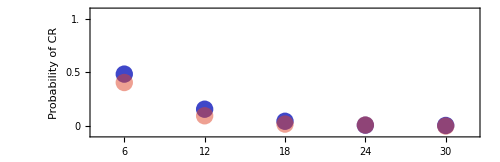

/Users/altrock/Dropbox/Projects_Dropbox/CART/code/hybridModelRuns/WTcell_Prob01.pdf

```mathematica
WTPFS={L2[WTPFSrB065,ColorData["Rainbow"][0.15],1],L2[WTPFSrB165,Opacity[0.5,ColorData["Rainbow"][0.95]],2]};
fig2WT=Show[WTPFS]
Export[NotebookDirectory[]<>"WTcell_Prob01.pdf",fig2WT,"PDF"]
```